```mathematica
(*This program uses binomial trees to price European call options
*)


(*Calibration of parameters
-Chosing d=1/u gives a symmetric random walk (SRW). This reduces the number of entries of the matrix (each row only has one more entry than the previous one).
-Instead of $1+r, 1+a, 1+b$ we write $exp(rdelta), u,1/u$ with $u=exp(sigma*sqrt[delta])$.
*)
T=1;
delta[n_]:=T/n;
u[n_,sigma_]:=Exp[sigma*Sqrt[delta[n]]];
d[n_,sigma_]:=1/u[n,sigma];
p[n_,sigma_,r_]:=(Exp[r*delta[n]]-d[n,sigma])/(u[n,sigma]-d[n,sigma]);

(*Build stock price tree
-It builds a lower triangular matrix, check for example with MatrixForm.
-If we define Table[expr(i,j),{i,n},{j,i}], the entries of the matrix, i.e. if we write stockTree[[i,j]] will range from i=1,n and j=1,i. Moreover, epr(i,j) is assigned to stockTree[[i,j]].
-If we had defined Table[expr(i,j),{i,0,n},{j,0,i}] the entries of the matrix would  range from i=1,n+1 and j=1,i. This would cause that expr(i,j) is not assigned to stockTree[[i,j]].
*)
stockTree[n_,sigma_,S0_]:=Table[S0*u[n,sigma]^(j-1)*d[n,sigma]^(i-j),{i,n},{j,i}];

(*Build payoff function for European call recursively:
-We build a function europeanCall (depending on n,sigma,s0,K and r) which yields the option price.
-Define it as a module (stockT,OptionT) are local variables. 
-StockT is already defined, we just have to define Option T.
-We first initialize OptionT by building a table whose entries are given by the payoff function. This already gives the correct entries of Option T corresponding to $i=n$.
-We then redefine the entries with $i<n+1$ by backward induction.
-Thinking of the lower diagonal nature of the matrix helps to see how to define the backwards induction.
*)
europeanCall[n_,sigma_,S0_,K_,r_]:=Module[{stockT=stockTree[n,sigma,S0],optionT},
(*Initialize option tree at maturity*)optionT=Table[Max[0,stockT[[i,j]]-K],{i,n},{j,i}];
(*Backward induction*)Do[optionT[[i,j]]=Exp[-r*delta[n]]*(p[n,sigma,r]*optionT[[i+1,j+1]]+(1-p[n,sigma,r])*optionT[[i+1,j]]),{i,n-1,1,-1},(*Backwards in time*){j,1,i}        (*For each node at this time step*)];
(*Return option price at t=0*)optionT[[1,1]]];

(*It is interesting to see how the price moves as we change K. For example the option price will be zero if K is larger than S0 u^n*)
 europeanCall[500,0.01,100,100*(u[500,0.01])^(20),0.05]
```

4.01284

6.09819×10^-7

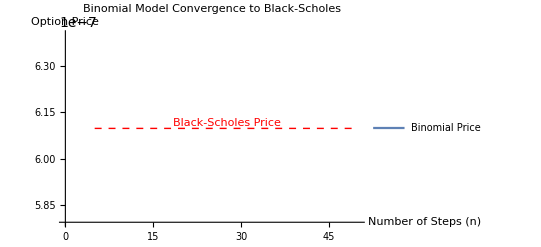

```mathematica
(*Black-Scholes Formula for European Call*)
blackScholesCall[S0_,K_,r_,sigma_,T_]:=Module[{d1,d2},d1=(Log[S0/K]+(r+0.5*sigma^2)*T)/(sigma*Sqrt[T]);
d2=d1-sigma*Sqrt[T];
S0*CDF[NormalDistribution[],d1]-K*Exp[-r*T]*CDF[NormalDistribution[],d2]]; (* This is the Black-Scholes formula. CDF[law,x] yields the cumulative distribution at x  of the rv with law*)

(*Parameters
-NO ARBITRAGE: Choose sigma>r*sqrt[delta] (see above)
*)
sigma=0.01;S0=100;K=100;r=0.05;
bsPrice=blackScholesCall[S0,K,r,sigma,T]

(*Compare with binomial model for different n values*)
nValues=Range[5,50,5];(*Test n from 5 to 200 in steps of 5*)
binomialPrices=Table[{n,europeanCall[n,sigma,S0,K,r]},{n,nValues}];

(*Plot convergence*)
ListPlot[binomialPrices,Joined->True,PlotRange->{Automatic,{bsPrice*0.95,bsPrice*1.05}},Epilog->{Red,Dashed,Line[{{Min[nValues],bsPrice},{Max[nValues],bsPrice}}],Text["Black-Scholes Price",{Mean[nValues],bsPrice},{0,-1}]},
AxesLabel->{"Number of Steps (n)","Option Price"},PlotLabel->"Binomial Model Convergence to Black-Scholes",PlotLegends->{"Binomial Price","Black-Scholes Price"}]
```